```mathematica
(*Задача 1*)
f[x1_, x2_] =x1+2×x2;
```

```mathematica
(*Обмеження*)
```

```mathematica
X={-x1+x2≤ 3, 3x1+x2≤ 11, 3x1+5x2≥7};
Print["Обмеження X: ",X//TableForm]
For[i=1, i≤ Length[X], i++,
{
If[MemberQ[{X[[i]]},_GreaterEqual]== True, 
{X[[i]]= (Expand[-X[[i,1]]]≤ -X[[i,2]])}]
}];
kTab=Table[(-Coefficient[X[[i,1]],x1])/Coefficient[X[[i,1]],x2],{i,1,Length[X]}];
bTab=Table[X[[i,2]]/Coefficient[X[[i,1]],x2],{i,1,Length[X]}];
XNew={};
For[i=1, i≤ Length[X], i++,
{
If[Coefficient[X[[i,1]],x2]<0, AppendTo[XNew, x2≥ kTab[[i]] x1 +  bTab[[i]]], AppendTo[XNew, x2≤ kTab[[i]] x1 +  bTab[[i]]]]
}];
Print["Обмеження X новий вигляд: ",XNew//TableForm]
```

Обмеження X: -x1+x2≤3
3 x1+x2≤11
3 x1+5 x2≥7

Обмеження X новий вигляд: x2≤3+x1
x2≤11-3 x1
x2≥7/5-(3 x1)/5

```mathematica
XPlot=Table[XNew[[i,2]],{i,1,Length[XNew]}]/.x1->x
RegXPlot=Table[XNew[[i]],{i,1,Length[XNew]}]/.{x1->x,x2->y}
```

{3+x,11-3 x,7/5-(3 x)/5}

{y≤3+x,y≤11-3 x,y≥7/5-(3 x)/5}

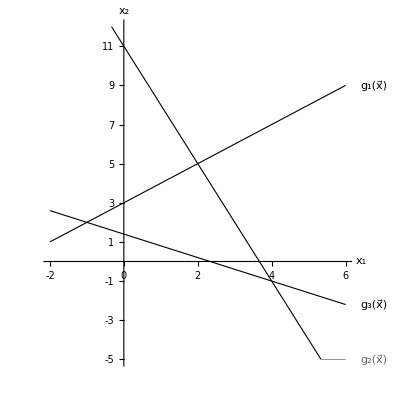

```mathematica
Gr=Plot[{3+x,11-3 x,7/5-(3 x)/5}, {x, -2,6}, PlotRange->{-5,Max[bTab]+1}, PlotStyle->Directive[Black, Thickness[0.002]], AxesStyle ->Directive[Black,Arrowheads[0.02]],AxesLabel->{Subscript[x, 1], Subscript[x, 2]}, PlotLabels->{"g_1(x⃗)","g_2(x⃗)", "g_3(x⃗)"}, Ticks->{Table[i, {i, -2, 6}],Table[i, {i, -5, 11}]},AspectRatio->1](*Масив графиків міняти,
PlotRange, x міняти*)
```

```mathematica
(*Лінії рівня*)
```

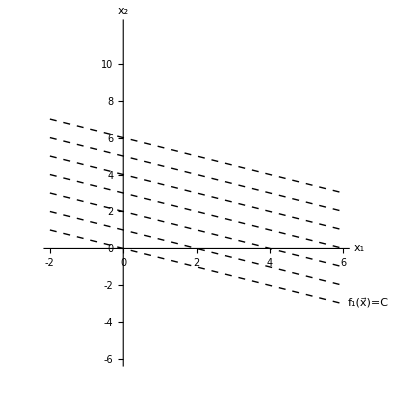

```mathematica
r[x_, c_] =(-Coefficient[f[x,y],x])/Coefficient[f[x,y],y] x+ c/Coefficient[f[x,y],y];
tab = Table[r[x, c], {c, 0,Max[bTab]+1, Coefficient[f[x,y],y]}];
linesLev=Plot[tab, {x, -2, 6}, PlotRange->{-6,Max[bTab]+1}, AspectRatio->1, PlotStyle->Directive[Black, Dashed, Thickness[0.0025]], AxesStyle ->Directive[Black,Arrowheads[0.02]],AxesLabel->{Subscript[x, 1], Subscript[x, 2]},  PlotLabels->Placed[{"f_1(x⃗)=C"},After], Ticks->{Table[i, {i, -2, 6}],Table[i, {i, -6, 11}]}]
```

```mathematica
(*Знаходимо автоматично точки екстремуму*)
min=Minimize[{f[x,y],RegXPlot[[1]]&&RegXPlot[[2]]&&RegXPlot[[3]]}, {x, y}][[1]];
Xmin=Minimize[{f[x,y],RegXPlot[[1]]&&RegXPlot[[2]]&&RegXPlot[[3]]}, {x, y}][[2,;;,2]];
max=Maximize[{f[x,y],RegXPlot[[1]]&&RegXPlot[[2]]&&RegXPlot[[3]]}, {x, y}][[1]];
Xmax=Maximize[{f[x,y],RegXPlot[[1]]&&RegXPlot[[2]]&&RegXPlot[[3]]}, {x, y}][[2,;;,2]];
Print["Умовний мінімум = ", min, "\nТочка min = ", Xmin,
"\nУмовний max = ", max, "\nТочка max = ",Xmax]
```

Умовний мінімум = 2
Точка min = {4,-1}
Умовний max = 12
Точка max = {2,5}

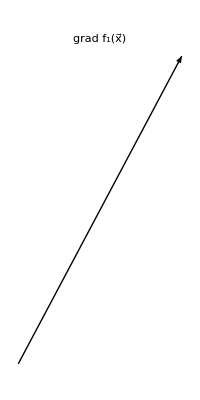

```mathematica
Graphics[Arrow [{{0,0},Grad[f[x1,x2],{x1, x2}]}],PlotLabel->"grad f_1(x⃗)"]
```

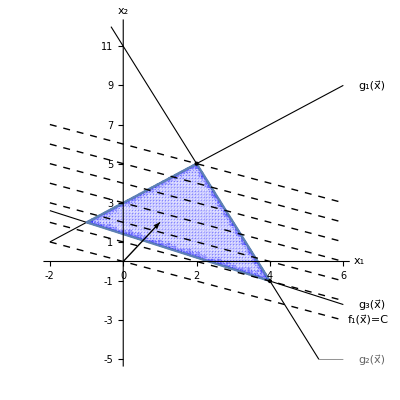

```mathematica
show=Show[Gr, RegionPlot[RegXPlot[[1]]&&RegXPlot[[2]]&&RegXPlot[[3]],{x,-2,6},{y,-4,12},PlotStyle->Opacity[0.1,Blue],PlotPoints->100,MaxRecursion->5],
Graphics[Arrow [{{0,0},Grad[f[x1,x2],{x1, x2}]}],PlotLabel->"grad f_1(x⃗)"],
linesLev, 
Epilog-> {PointSize[Medium],Point[{Xmin, Xmax}]}](*Суміщаємо лінії рівня та область обмеження*)
```

```mathematica
Line1=Graphics[{Thick,Dashed,Red,Line[{{0, Xmax[[2]]},Xmax}]}];
Line2=Graphics[{Thick,Dashed,Red,Line[{{Xmax[[1]],0},Xmax}]}];
Line3=Graphics[{Thick,Dashed,Red,Line[{{0, Xmin[[2]]}, Xmin}]}];
Line4=Graphics[{Thick,Dashed,Red,Line[{{Xmin[[1]],  0}, Xmin}]}];
```

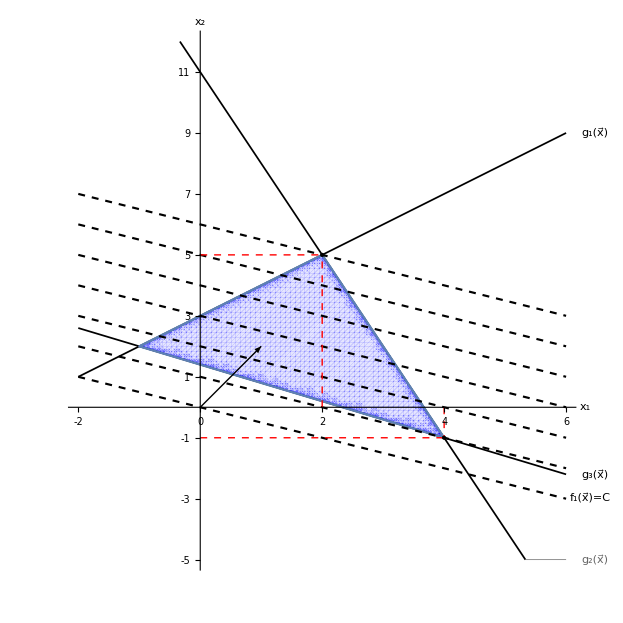

```mathematica
Show[show, Line1,Line2, Line3, Line4]
```

```mathematica
(*Задача 2*)
F[x_,y_]=(x+1)^2+(y+2)^2;
center=Table[0,2];
For[j=1, j≤ 2, j++,
{
If[MemberQ[{F[x,y][[j,1]]},_Plus]==True,
center[[j]]=-F[x,y][[j,1,1]], 
center[[j]]=F[x,y][[j,1,1]]];
}];
R=8; (*Максимальний радіус кола*)
tab=Join[Table[Circle[center, i], {i, 0,R,.5}],{Circle[center, 3.37]}]; (*Міняти кола в залежності від функції цілі та загального графіка*)
cir=Graphics[{Dashed,tab},Axes->True, AxesStyle ->Directive[Black,Arrowheads[0.02]],AxesLabel->{Subscript[x, 1], Subscript[x, 2]}, Ticks->{Table[i, {i, -9, 7}],Table[i, {i, -6, 11}]},AspectRatio->1, PlotRange-> {{-11.2, 11.2}, {-11.2, 11.2}}, PlotLabel-> "f_2(x⃗)=C"]
```

-Graphics-

```mathematica
(*Знаходимо автоматично точки екстремуму*)
min=Minimize[{F[x,y],RegXPlot[[1]]&&RegXPlot[[2]]&&RegXPlot[[3]]}, {x, y}][[1]];
Xmin=Minimize[{F[x,y],RegXPlot[[1]]&&RegXPlot[[2]]&&RegXPlot[[3]]}, {x, y}][[2,;;,2]];
max=Maximize[{F[x,y],RegXPlot[[1]]&&RegXPlot[[2]]&&RegXPlot[[3]]}, {x, y}][[1]];
Xmax=Maximize[{F[x,y],RegXPlot[[1]]&&RegXPlot[[2]]&&RegXPlot[[3]]}, {x, y}][[2,;;,2]];
Print["Умовний мінімум = ", min, "\nТочка min = ", Xmin,
"\nУмовний max = ", max, "\nТочка max = ",Xmax]
```

Умовний мінімум = 200/17
Точка min = {13/17,16/17}
Умовний max = 58
Точка max = {2,5}

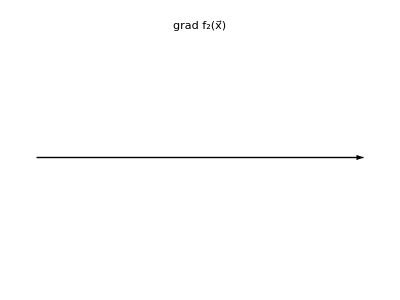

```mathematica
Graphics[Arrow [{{center[[1]]+R,center[[2]]},{center[[1]]+R+2,center[[2]]}}],PlotLabel->"grad f_2(x⃗)"]
```

```mathematica
Print["Графічний метод знаходження екстремумів: "]
Show[cir,Gr,RegionPlot[RegXPlot[[1]]&&RegXPlot[[2]]&&RegXPlot[[3]],{x,-2,6},{y,-4,12},PlotStyle->Opacity[0.1,Blue],PlotPoints->100,MaxRecursion->5, AspectRatio->1],
Graphics[Arrow [{{center[[1]]+R,center[[2]]},{center[[1]]+R+2,center[[2]]}}],PlotLabel->"grad f_2(x⃗)"], 
Epilog-> {Red,PointSize[.005],Point[{Xmin, Xmax, center}]}]
```

Графічний метод знаходження екстремумів:

-Graphics-

Аналітичний спосіб розрахунків
Треба дивитися за графіком, які прямі-обмеження перетинаються з функціями цілі

```mathematica
kF=-D[F[x1,x2],x1]/D[F[x1,x2],x2];
Print["k_f_2 = ", kF];
kg3=kTab[[3]];
Print["k_g_3 = ",kg3]
A=Table[Solve[{kF==kg3, (XPlot[[3]]/.x->x1)== x2},{x1,x2}][[1,i,2]],{i,1,2}];
Print["Точка мінімуму A = ", A]
Print["Умовний мінімум A = ", F[A[[1]], A[[2]]]]
B=Table[Solve[{XPlot[[1]]==y, XPlot[[2]]== y},{x,y}][[1,i,2]],{i,1,2}];
Print["Точка максимуму B = ", B]
Print["Умовний максимум B = ", F[B[[1]], B[[2]]]]
```

k_f_2 = -(1+x1)/(2+x2)

k_g_3 = -3/5

Точка мінімуму A = {13/17,16/17}

Умовний мінімум A = 200/17

Точка максимуму B = {2,5}

Умовний максимум B = 58